关联

关联是列表的一种推广形式，其中每个元素都有一个键值和一个值。Counts 是一个典型的生成关联的函数。

Counts 将给出一个关联，报告每个不同元素出现的次数：

```mathematica
Counts[{a,a,b,c,a,a,b,c,c,a,a}]
```

<|a→6,b→2,c→3|>

你可以使用 [...] 来获取与某个特定键值相关联的值。

找出关联中与 c 相关联的值：

```mathematica
<|a->6,b->2,c->3|>[c]
```

3

适用于列表的操作通常也适用于关联，但只是应用于值，而不是键值。

这将把关联中的每个值都增加 500：

```mathematica
<|a->6,b->2,c->3|>+500
```

<|a→506,b→502,c→503|>

/@ 是将一个函数应用于关联中的每个值：

```mathematica
f/@<|a->6,b->2,c->3|>
```

<|a→f[6],b→f[2],c→f[3]|>

Total 将给出值的总和：

```mathematica
Total[<|a->6,b->2,c->3|>]
```

11

Sort 也是对值进行操作：

```mathematica
Sort[<|a->6,b->2,c->3|>]
```

<|b→2,c→3,a→6|>

KeySort 是对键值进行排序：

```mathematica
KeySort[<|c->1,b->2,a->4|>]
```

<|a→4,b→2,c→1|>

函数 Keys 和 Values 用于提取一个关联的键值和值列表。

获取关联中的键值列表：

```mathematica
Keys[<|a->6,b->2,c->3|>]
```

{a,b,c}

获取关联中的值列表：

```mathematica
Values[<|a->6,b->2,c->3|>]
```

{6,2,3}

Normal 将把一个关联转换为一个正常的规则列表。Association 将使用一个规则列表来创建关联。

```mathematica
Normal[<|a->6,b->2,c->3|>]
```

{a→6,b→2,c→3}

```mathematica
Association[{a->6,b->2,c->3}]
```

<|a→6,b→2,c→3|>

LetterCounts 用于计算字母在一个字符串中出现的次数。

计算每个字母在维基百科上关于计算机的文章中出现了多少次：

```mathematica
LetterCounts[WikipediaData["computers"]]
```

<|e→4833,t→3528,a→3207,o→3059,r→2907,i→2818,n→2747,s→2475,c→1800,l→1673,m→1494,h→1473,u→1357,d→1329,p→1153,g→818,f→766,y→594,b→545,w→456,v→391,k→174,T→150,A→110,I→101,C→84,M→82,x→77,S→68,P→64,q→58,U→55,B→45,H→43,E→42,R→41,L→41,z→38,O→38,D→37,W→30,N→29,F→28,j→25,G→23,J→17,K→14,V→10,Z→8,Q→4,ū→4,ī→4,ö→2,ā→2,Y→1,X→1,é→1,â→1|>

KeyTake 用于取出关联中出现在你指定的键值列表中的元素。在这个例子中，我们要取出键值为小写英文字母的元素。

只取出关联中键值为小写字母的元素：

```mathematica
KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]]
```

<|a→3207,b→545,c→1800,d→1329,e→4833,f→766,g→818,h→1473,i→2818,j→25,k→174,l→1673,m→1494,n→2747,o→3059,p→1153,q→58,r→2907,s→2475,t→3528,u→1357,v→391,w→456,x→77,y→594,z→38|>

BarChart 可以用于绘制关联中的数值。使用选项 ChartLabels→Automatic，则将使用键值作为标签。

将每个字母出现的次数绘制为条形图；“e”是最常见的：

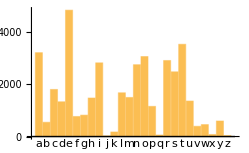

```mathematica
BarChart[KeyTake[LetterCounts[WikipediaData["computers"]],Alphabet[ ]],ChartLabels->Automatic]
```

这里有一个直接将纯函数应用于关联的方法：

将纯函数应用于关联：

```mathematica
f[#["apples"],#["oranges"]]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

键值为字符串是很常见的，当涉及到纯函数时，Wolfram 语言有一个特殊的方法来处理这些：你可以直接用 #key 来指代键值为“key”的元素。

对于键值为字符串的关联元素，使用更简单的符号表示：

```mathematica
f[#apples,#oranges]&[<|"apples"->10,"oranges"->12,"pears"->4|>]
```

f[10,12]

一个更现实的例子，应用一个纯函数，从字母计数中取出“e”的值，然后除以总数。N 将使给出的结果是一个小数。

计算关于“计算机”的文章中字母“e”所占的比例：

```mathematica
#e/Total[#]& @LetterCounts[WikipediaData["computers"]]//N
```

0.11795

词汇

<|key_1→value_1,key_2→value_2, ...|> |   | 一个关联
Association[rules] |   | 将规则列表转换为关联
assoc[key] |   | 取出关联中的元素
Keys[assoc] |   | 关联中的键值列表
Values[assoc] |   | 关联中的值列表
Normal[assoc] |   | 将关联转换为规则列表
KeySort[assoc] |   | 按关联的键值对其进行排序
KeyTake[assoc,keys] |   | 取出特定键值的元素
#key |   | 键值为“key”的元素的函数槽
Counts[list] |   | 包含不同元素数量的关联
LetterCounts[string] |   | 包含不同字母数量的关联

"共有 6 道习题" | "开始练习 »"

按顺序列出 3^100 中 0 到 9 在每位数字中出现的次数。»

| 期望输出： |  
  | {7,9,9,5,1,5,4,7,1} |

将 2^1000 中 0 到 9 在每位数字中出现的次数创建为一个有标签的条形图。»

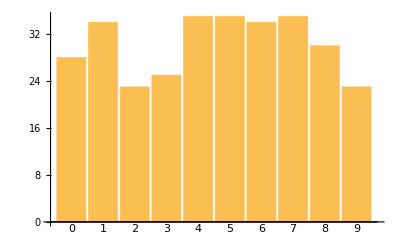
| 期望输出： |  
  | -Graphics- |

将 WordList[ ] 中的每个单词可能的首字母出现的次数创建为一个有标签的条形图。»

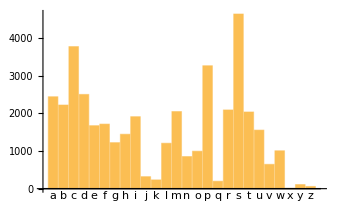
| 期望输出： |  
  | -Graphics- |

创建一个关联，给出 WordList[ ] 中 5 个最常见的单词首字母与它们的数量。»

| 期望输出： |  
  | <|"s"→4642,"c"→3776,"p"→3267,"d"→2504,"a"→2443|> |

在维基百科上关于计算机的词条中找出 “q” 和 “u” 的出现次数的比值。»

| 期望输出示例： |  
  | 0.0426784 |

在 ExampleData[{"Text","AliceInWonderland"}] 中找出 10 个最常见的单词。»

| 期望输出： |  
  | {"the","and","a","to","she","of","was","Alice","in","it"} |

问&答

为什么叫“关联”这个名字？

因为它们将值与键值相关联。用于同一概念的其他名称是关联数组、字典、哈希映射、结构、键值映射以及符号索引列表。

如何输入一个关联？

从 <| (< 后跟 |)开始，然后使用 -> 来表示每个 →。也可以使用 Association[a->1,b->2]。

一个关联中能否包含多个具有相同键值的元素？

不可以。关联中的键值总是唯一的。

如果我要求的键值不在一个关联中，会发生什么？

通常你会得到 Missing[...]。但是如果你使用 Lookup 来查找键值，你可以指定在键值不存在时返回什么。

我怎样才能对一个关联的键值进行操作？

使用 KeyMap，或者使用像 KeySelect 和 KeyDrop 这样的函数。AssociationMap 通过将一个函数映射到键值上来创建一个关联。

我怎样将几个关联合并为一个？

使用 Merge。你必须给出一个函数，指出如果在多个关联中出现同一个键值该怎么做。

能否使用 [[...]] 来提取关联的一部分，就像提取列表的一部分一样？

是的，如果你明确指出 assoc[[Key[key]]]。例如，assoc[[2]] 将取出 assoc 的第二个元素，不管它的键值是什么。assoc[[key]] 是一种特殊情况，工作原理与 assoc[key] 相同。

如果一个关联中的键值不是字符串，那么在纯函数中会发生什么？

你不能再使用 #key，你必须明确地使用 #[key]。

技术笔记

大多数函数对关联的操作就像它们直径对其值的列表进行操作一样高效。在列表逐项作用的函数通常也会在关联上进行同样的操作。

关联就像关系型数据库中的表。JoinAcross 做的是类似于数据库的连接操作。

探索更多

Wolfram 语言中的关联指南 »